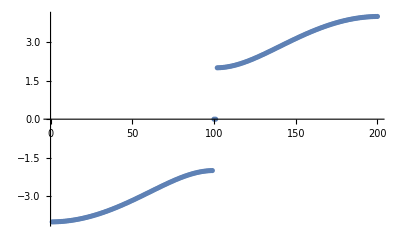

```mathematica
t=1;
t2=3;
n=100;
H=N[Table[t*KroneckerDelta[i+n,j]+t*KroneckerDelta[j+n,i]+t2*KroneckerDelta[i+n+1,j]+t2*KroneckerDelta[j+n+1,i],{i,1,2n},{j,1,2n}]];
ListPlot[Sort[Eigenvalues[H]]]
```

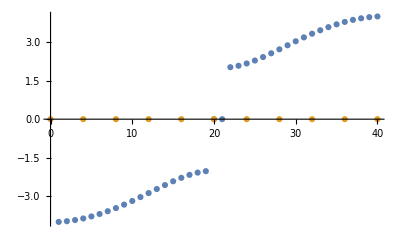

```mathematica
n=20;
t2=3;
t1=1;
H=N[Table[t*KroneckerDelta[i+n,j]+t*KroneckerDelta[j+n,i]+t2*KroneckerDelta[i+n+1,j]+t2*KroneckerDelta[j+n+1,i],{i,1,2n},{j,1,2n}]];
H2[U_]:=N[Table[t*KroneckerDelta[i+n,j]+t*KroneckerDelta[j+n,i]+t2*KroneckerDelta[i+n+1,j]+t2*KroneckerDelta[j+n+1,i]+U*KroneckerDelta[i,1]*KroneckerDelta[j,1],{i,1,2n},{j,1,2n}]];
ListPlot[{Sort[Eigenvalues[H]],Table[{U*(n/5),Abs[Sort[Eigenvalues[H2[U]]][[n]]]},{U,0,10,1}]}]
```